### Photodiode Pixel Counting

```mathematica
FSR=6*25;
c=3*10^11;
λ=635*10^-6;
L=200+Sqrt[200^2+75^2];
ArcTan[75/200]*180/Pi;
FSRcalc=N[c/(2L)/10^6];(*MHz*)
R=1000;
cavityWaist=Sqrt[λ/Pi Sqrt[L R]Sqrt[1-L/R]];
Print["FSR: ",FSR, "MHz"]
Print["Cavity Waist: ", N[cavityWaist], "mm"]
```

FSR: 150MHz

Cavity Waist: 0.315504mm

```mathematica
FSRpixels={1618,1319,1572,1302,1521,1349};
linewidthpixels={37,57,47,45,40,50};
finesse=N[Mean[FSRpixels]/Mean[linewidthpixels]];
FSR=Mean[FSRpixels];
linewidth=Mean[linewidthpixels];
ΔFSR=N[StandardDeviation[FSRpixels]/Sqrt[6]];
Δlinewidth=N[StandardDeviation[linewidthpixels]/Sqrt[6]];
Δfinesse=finesse*Sqrt[(ΔFSR/FSR)^2+(Δlinewidth/linewidth)^2-2*(ΔFSR/FSR)(Δlinewidth/linewidth)];
Print["Finesse: ",finesse,"+/-",Δfinesse]
Print["Linewidth: ",FSRcalc/finesse,"+/-",FSRcalc/finesse*(Δfinesse/finesse)]
```

Finesse: 31.4529+/-0.758989

Linewidth: 11.5305+/-0.278243

### Mode Matching Calculations

{w0→0.01081,d→57.0879}

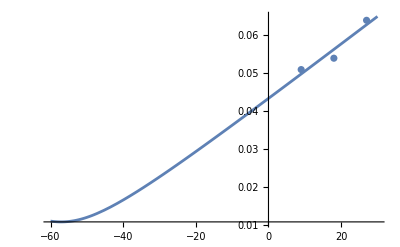

```mathematica
pos={9,18,27};
wx={.51,.54,.64}/10;
data2=Transpose@{pos,wx};
λ=2.5*10^-5;
w[z_]:=w0 Sqrt[(1+((z+d) λ/(Pi w0^2))^2)];
vars2=FindFit[data2,w[x],{{w0,.4},{d,-1}},x,Method->NMinimize]
wfit2[x_]=w[x]/.vars2;
Show[Plot[wfit2[x],{x,-60,30}],ListPlot[data2],PlotRange->All]
wminy=vars2[[1,2]];
posminy=vars2[[2,2]];
```

```mathematica
M[iq_,A_]:=(A[[2,1]]+A[[2,2]]*iq)/(A[[1,1]]+A[[1,2]]*iq);
lensprop[f_,L_]:=({{1, L}, {0, 1}}).({{1, 0}, {-1/f, 1}});
Rad[iq_]:=1/Re[iq];
waist[iq_]:=1/Sqrt[-Im[iq]*Pi/λ];
Mfree[L_]:=({{1, L}, {0, 1}});
Mlens[f_]:=({{1, 0}, {-1/f, 1}});
inq[z_,w_]:=1/(z(1+(Pi w^2/λ/z)^2))-I λ/(Pi w^2(1+(z λ/(Pi w^2))^2));
inqw[w_]:=-I λ/(Pi w^2);
```

```mathematica
(telescope=Mfree[388].Mlens[50].Mfree[235].Mlens[150].Mfree[508])//N//MatrixForm
```

(1.244 | -568.648
0.00466667 | -1.32933)

```mathematica
iq=inqw[wfit2[-43.5]*25.4];
cq=M[iq,telescope];
Print["Waist at cavity: ",waist[cq],"mm"]
Print["Radius of Curvature at cavity: ",Rad[cq],"mm"]
```

Waist at cavity: 0.557645mm

Radius of Curvature at cavity: 301.006mm